# GMRES Generalized Minimum Residual

We are going to iteratively approximate the solution of 
	A.x=b
using the Krylov space
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
The polynomial 
	q(A)=c_0 Id+c_1 A+ c_2 A^2+…+c_(n-1)A^(n-1) 
(remember x∈𝒦_n(A,b)  satisfies x=c_0 b+c_1 A.b+ c_2 A^2.b+…+c_(n-1)A^(n-1).b=q(A).b) is going to make another appearance and the target x_exact=A^-1.b satisfies A.x_exact=b.

## Arnoldi Reminder

Just as a reminder: The Arnoldi process iteratively computes a nested sequence of orthogonal matrices Q_n∈ℝ^(m×n) and rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n).  Columns of Q_n are an orthonormal basis for the Krylov space	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By construction, A maps 𝒦_n(A,b)→𝒦_(n+1)(A,b) with H_n the matrix for this map in the orthogonal basis. In other words, since H_n is Upper Hessenberg
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
If the bottom corner of H_n is zero the Q_n is an invariant space of A.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Remember:

Q_n is an orthogonal basis for the something approximating the “large” eigenspace of A

Q_(n+1)=[Q_n|q_(n+1)]

By construction multiplying by A maps 𝒦_n→𝒦_(n+1) and the map is expressed by H_n

H_n=((Ĥ)_n
0,…,0,H_(n+1,n)) is a rectangular Hessenberg matrix.

## GMRES

The GMRES approximation is simply
	x_n=argmin_(x∈𝒦_n)||A.x-b||
We have a convenient basis for 𝒦_n so we write x_n=Q_n.y_n and note that
	y_n=argmin_(y∈ℝ^n)||A.Q_n.y-b||=argmin_y||Q_(n+1).H_n.y-b||
In words, y_n is the best solution in 𝒦_n and the Arnoldi construction lets us explicitly flip things into the one larger space. We are nearly done remember b∈𝒦_(n+1) and (Q_(n+1))ᵀ.b=e_1 and Q_(n+1) is orthogonal so
		y_n=argmin_y||Q_(n+1).H_n.y-b||=argmin_y||H_n.y-(Q_(n+1))ᵀ.b||=argmin_y||H_n.y-||b||e_1||
The last problem is a small linear least squares problem with an almost triangular right hand side.

Since we already have Arnoldi code this will be pretty easy to code.

The question is how fast does it converge?

The residuals r_n=b-A.x_n satisfy
	||r_n||=min_(x∈𝒦_n) ||A.x-b||=min_(y∈ℝ^n) ||H_n.y-||b||e_1||

||r_(n+1)||≤||r_n|| since 𝒦_(n+1)⊃𝒦_n.

The residuals are given by polynomials in A i.e.
	x_n=(c_1 A^0+c_2 A^1+…+c_n A^(n-1)).b

r_n=b-A.x_n=(I_m-A.(c_1 A^0+c_2 A^1+…+c_n A^(n-1))).b

By definition, GMRES produces best optimal polynomial in the space 𝒫_n^GMRES={1+a_1 z+…+a_n z^n}.

p_n^GMRES=argmin_(p∈𝒫_n^GMRES)|| p(A).b||

Since we run out of dimensions when n=m we know that r_m=0.

The induced matrix norm satisfies ||p(A).b||≤||p(A)(||)_induced||b|| for any polynomial. So we have

(||r_n||)/(||b||)=(||p_n^GMRES(A).b||)/(||b||)≤(||p(A).b||)/(||b||)≤||p(A)(||)_induced  for any p∈𝒫_n^GMRES

If A lets us pick polynomials p∈𝒫_n^GMRES with p(A) small then we know the residuals get small fast.

We are going to come back to this once we see the GMRES in action.

## GMRES in Action.

## Arnoldi is “Optimal”

The Arnoldi process produces the best monic (lead coefficient equals one) polynomial in the sense that 
	𝓅_n(z)=det(z I-(Ĥ)_n)=argmin_(p∈𝒫_n)||p(A).b||
 where 𝒫_n={z^n+c_(n-1)z^(n-1)+…+c_2 z^2+c_1 z+c_0}.  This looks weird but it is just orthogonality in the Arnoldi process and the Cayley-Hamilton (CH) theorem “Matrices satisfy their  own characteristic polynomial”.

p(A).b=A^n.b-Q_n.y for p∈𝒫_n and some y∈ℂ^n. So
	argmin_(p∈𝒫_n)||p(A).b|| | ⟺ | y_best=argmin_(y∈ℂ^n)||A^n.b-Q_n.y||.

The point in 𝒦_n(A,b) nearest A^n.b is simply y_best=(Q_n)†.A^n.b.

The minimum value is ||(I_m-Q_n.(Q_n)†).A^n.b||

Continuing Arnoldi would give the Hessenberg decomposition 
	A=Q_m.(Ĥ)_m.(Q_m)†

Q_m=[Q_n | | | Q_rest]  and (Ĥ)_m[1:n+1,1:n]=H_n

p(A)=P(Q_m.(Ĥ)_m.(Q_m)†)=Q_m.p((Ĥ)_m).(Q_m)†

So y_best=(Q_n)†.Q_m.((Ĥ)_m)^n.(Q_m)†.b tidies up (because 
(Q_n)†.Q_m=(I_n | | | 0_(n×m)) and (Q_m)†.b=(Q_m)†.q_1= e_1) to 
	y_best=(I_n|0_(n×m) ).((Ĥ)_m)^n.e_1=((Ĥ)_m)^n⟦1:n,:⟧.e_1=((Ĥ)_n)^n.e_1

In words, the optimal y is the first column of the nth power of (Ĥ)_n!

The characteristic polynomial gives ((Ĥ)_n)^n.

## Using Arnoldi “Optimality”

We know that any other polynomial gives a bigger value! for any monic polynomial p_n∈𝒫_n of the correct power
	||p_n(A).b||≥||𝓅_n(A).b||=c_n. 
This is surprisingly useful if we approximate 𝓅_n .If we are interested in the convergence to the large real eigenvalue λ≈1.3 after a while we can pick out the eigenvalue of (Ĥ)_n that is converging to λ. We have λ_n→λ and choose 
 	p_n(z)=z^(n-1)(z-λ_n)
 which is small on the unit circle (where all the other eigenvalues live) and zero at z=λ_n. It is a crude approximation to the characteristic polynomial.  Near z=λ_n we have 
 	|p_n(z)|~|λ_n|^(n-1)|z-λ_n|∼1.3^n|z-λ_n|
 which has one term that gets big.  If 
 	|p_n(λ)|∼Mc_n then 1.3^n|λ-λ_n|∼M c_n 
 and we would get the estimate
 	 1.3^n|λ-λ_n|∼(1/1.3)^n M c_n 
which indicates geometric convergence. Lets see if we can see this happen.

```mathematica
m=400;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.3,0.2,0.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
λBig=Eigenvalues[A,1]⟦1⟧
```

1.25293+0. ⅈ

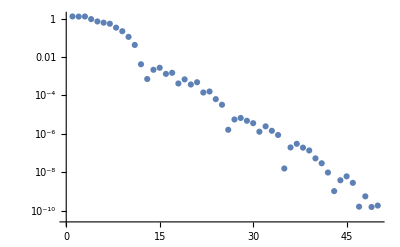

```mathematica
MaxIter=50;
b=Normalize[RandomReal[{-1,1},m]];
{Q,H}={{b}ᵀ,{{}}};
ListLogPlot[
Table[
{Q,H}=Arnoldi[A][{Q,H}];
Abs[λBig-Eigenvalues[Drop[H,-1],1]⟦1⟧],
{MaxIter}]]
```

It does indeed converge geometrically linearly.  The slope depends on the gap between the largest eigenvalue and the rest of the spectrum.  You need to be sneakier to understand the convergence to a complex conjugate pair.